# Introdução à Física Computacional I (2023.2)

## Aula 2: manipulação algébrica; funções definidas pelo usuário; gráficos simples Parte de 2-2 e 2-3 por conta dos gráficos

## Transformando expressões algébricas

Existem muitas funções no Mathematica para manipulação de expressões algébricas. Vamos listar aqui algumas delas, através de exemplos.

```mathematica
expr1 = (x-1)^2 *(2*x+7)*(5*x-3);
Expand[expr1] (* Expande todos os produtos e potências positivas *)
```

-21+71 x-69 x^2+9 x^3+10 x^4

```mathematica
expr2=(x-1)^4*(5*x-3)^3*(3*x^2+4*x-5);
Expand[expr2]
```

135-1323 x+5526 x^2-12694 x^3+17076 x^4-12764 x^5+3514 x^6+1830 x^7-1675 x^8+375 x^9

```mathematica
Factor[expr2/expr1] (* Fatora completamente o argumento *)
```

((-1+x)^2 (-3+5 x)^2 (-5+4 x+3 x^2))/(7+2 x)

```mathematica
expr3=(5*x^2-4*x+16)/((x^2-x+1)^2*(x-3));
Apart[expr3] (* Decompõe em frações parciais *)
```

1/(-3+x)+(-3-2 x)/((1-x+x^2)^2)+(-2-x)/(1-x+x^2)

```mathematica
expr4 = (y^2-5*y+4)/(y-1);
Cancel[expr4] (* Cancela fatores comuns *)
```

-4+y

```mathematica
Factor[y^2-5*y+4]
```

### Simplificando expressões

A função Simplify busca simplificar expressões algébricas, mas nem sempre atua da forma como desejamos, e é preciso recorrer a outras funções ou a opções adicionais.

```mathematica
expr5 = 1/(x^2-16)-(x+4)/(x^2-3*x-4);
```

```mathematica
Simplify[expr5]
```

(4+x)/(4+3 x-x^2)+1/(-16+x^2)

```mathematica
Together[expr5] (* Combina frações *)
```

(-15-7 x-x^2)/((-4+x) (1+x) (4+x))

A função Simplify aplica diversas transformações em busca da forma mais simples para uma expressão. Ainda mais transformações são aplicadas pela função FullSimplify, cuja execução, no entanto, pode demorar bem mais.

```mathematica
expr6=(Sqrt[(2+x)/(7+x)]*Sqrt[(3-x^2)/(25-x^2)]*Sqrt[(5+x)*(2-x)])/(Sqrt[4-x^2]*Sqrt[3-x^2])
```

(√((2-x) (5+x)) √((2+x)/(7+x)) √((3-x^2)/(25-x^2)))/(√(3-x^2) √(4-x^2))

```mathematica
Simplify[expr6]
```

(√((2+x)/(7+x)) √(10-3 x-x^2) √((-3+x^2)/(-25+x^2)))/(√(3-x^2) √(4-x^2))

```mathematica
FullSimplify[expr6]
```

1/(√(-((-5+x) (7+x))))

Algumas simplificações podem ser alcançadas indicando suposições, que são dadas como segundo argumento da função Simplify (ou de outras funções de manipulação algébrica).

```mathematica
expr7=Sqrt[x^2];
Simplify[expr7]
```

√(x^2)

```mathematica
Simplify[expr7,x>0] (* Supondo que x é positivo *)
```

x

```mathematica
Simplify[expr7,x∈Reals] (* Supondo que x é um número real *)
```

Abs[x]

```mathematica
Simplify[Log[x^r]]
```

Log[x^r]

```mathematica
Simplify[Log[x^r],x>0]
```

Log[x^r]

A função logaritmo é multivalorada se o argumento é complexo, de modo que, para obter a simplificação, temos que garantir que o argumento seja real. Para isso, usamos a construção abaixo:

```mathematica
Simplify[Log[x^r],x>0 && r∈Reals]
```

r Log[x]

Note que combinamos duas suposições (de que x é positivo e de que r pertence ao conjunto dos números reais) usando o operador lógico && (“e”). É uma construção que lembra bastante a notação matemática “escrita à mão”.

Funções intrínsecas que aceitam suposições, como Simplify, podem também ser invocadas como argumento da função intrínseca Assuming, cuja sintaxe é exemplificada abaixo:

```mathematica
Assuming[x>0,Simplify[Sqrt[x^2]]]
```

x

```mathematica
Assuming[x>0 && r∈Reals,Simplify[Log[x^r]]]
```

r Log[x]

### Transformando expressões trigonométricas

Para manipular expressões contendo funções trigonométricas, o Mathematica dispões de funções intrínsecas específicas. Os exemplos a seguir ilustram algumas delas:

```mathematica
TrigExpand[Cos[2*θ]] (* Expande em uma soma de termos *)
```

Cos[θ]^2-Sin[θ]^2

```mathematica
TrigReduce[Sin[θ]*Cos[θ]] (* Aplica identidades envolvendo múltiplos de ângulos *)
```

1/2 Sin[2 θ]

```mathematica
TrigFactor[Cos[2*θ]] (* Fatora em um produto de termos *)
```

2 Sin[π/4-θ] Sin[π/4+θ]

Outras funções intrínsecas úteis nesse contexto são as seguintes:

```mathematica
ComplexExpand[Cos[a+I*b]] (* Expande supondo que quaisquer variáveis são reais *)
```

```mathematica
ExpToTrig[Exp[I*θ]] (* Converte exponenciais em funções trigonométricas *)
```

Encontrar a função do Mathematica que produz a melhor simplificação para os seus objetivos pode ser bem complicado!

## Funções definidas pelo usuário

Além das muitas funções intrínsecas do Mathematica, você também pode definir suas próprias funções, usando a construção mostrada no exemplo a seguir.

```mathematica
f[x_]:=x+x^2
```

Há dois pontos a destacar aqui:

o argumento da função, na definição, é escrito seguido por uma “sublinha”, que indica que se trata de um argumento arbitrário, e não de uma variável x cujo valor tenha sido atribuído anteriormente;

a definição da função foi feita com “:=” em vez de uma igualdade simples, o que indica uma atribuição retardada, em que o cálculo é feito apenas quando a função for invocada.

## Atribuição retardada

Para ver o efeito da atribuição retardada, considere o exemplo a seguir.

```mathematica
k=10;
g[x_]=x+k*x^2; (* Note a ausência dos dois pontos na atribuição *)
h[x_]:=x+k*x^2; (* Note a presença dos dois pontos na atribuição *)
```

```mathematica
g[2]-h[2]
```

```mathematica
k=3;
g[2]-h[2]
```

Qual é a diferença de definição entre g[x] e h[x]?

E um segundo exemplo, agora sem que definamos uma função:

```mathematica
b=3;
a=b;
c:=b;
a-c
```

0

```mathematica
b=4;
a-c
```

## Substituições

Um recurso muito útil do Mathematica é a atribuição temporária oferecida pelo operador de substituição “/.” (sem as aspas). Vamos limpar a variável k,

```mathematica
Clear[k]
```

e redefinir a função f[x] como

```mathematica
f[x_]:=x+k*x^2
```

Formalmente, f[x] é função apenas de x, mas, enquanto k não for definido, claramente não é possível obter um valor puramente numérico para f[x]:

```mathematica
N[f[1]]
```

1.+k

O operador “/.” (também chamado de ReplaceAll) permite atribuir valores temporários a variáveis:

```mathematica
N[f[1]/.k-> 1/2]
```

1.5

Note a sintaxe que se segue ao operador “/.”: a atribuição temporária é feita não por meio da igualdade, mas pelo sinal “→” (obtido no modo de input pela sequência “->”).

Se agora consultarmos o valor de k, veremos que continua não estando atribuído:

```mathematica
k
```

k

Para mais um exemplo, vamos limpar as variáveis a, b e c,

```mathematica
Clear[a,b,c]
```

e redefinir mais uma vez a função f[x] como

```mathematica
f[x_]:=a*x^2+b*x+c
```

```mathematica
f[1]
```

a+b+c

A atribuição de valores temporários para a, b e c é feita pela sintaxe abaixo:

```mathematica
f[1]/.{a-> 1,b-> 2,c-> -1/2}
```

5/2

Note que a atribuição de mais de uma variável é feita entre chaves. Mais à frente, veremos que, na linguagem Wolfram, valores entre chaves definem uma lista, um importante tipo de estrutura de dados em muitas linguagens de programação.

Você pode definir uma “variável” para armazenar as atribuições temporárias, como no exemplo a seguir:

```mathematica
subs={a-> 1,b-> 2,c-> -1/2}
```

{a→1,b→2,c→-1/2}

```mathematica
f[1]/.subs
```

1+k

Uma forma alternativa de usar substituições envolve explicitamente a função ReplaceAll:

```mathematica
ReplaceAll[f[1],{a-> 1,b-> 2,c-> -1/2}]
```

5/2

Vou preferir a forma anterior, com “/.”, que não me parece induzir confusão e é mais compacta.

## Introdução às capacidades gráficas

A produção de gráficos no Mathematica pode ser feita de forma direta através da função Plot (e suas variantes que exploraremos em aulas futuras):

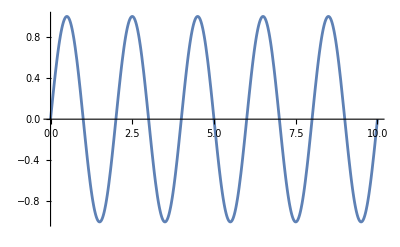

```mathematica
Plot[Sin[Pi*x],{x,0,10}]
```

Note a sintaxe: o primeiro argumento de Plot é a função cujo gráfico queremos produzir, e o segundo argumento (entre chaves) é uma lista que indica a variável que servirá de abscissa, seu valor inicial e seu valor final no gráfico.

Um segundo exemplo, utilizando substituições:

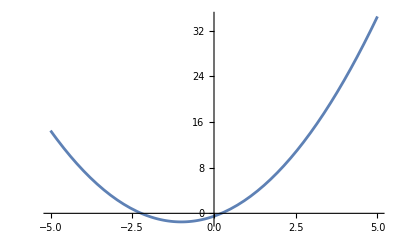

```mathematica
Plot[f[x]/.{a-> 1,b-> 2,c-> -1/2},{x,-5,5}]
```

E se quisermos mais de um gráfico no mesmo conjunto de eixos?

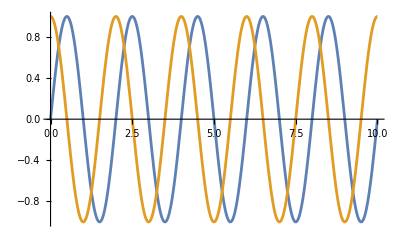

```mathematica
Plot[{Sin[π*x],Cos[π*x]},{x,0,10}]
```

Note que as funções a traçar devem estar entre chaves, formando uma lista.

Em aulas futuras, vamos explorar opções na linguagem Wolfram para dar uma aparência mais profissional aos gráficos e vamos discutir como traçar outros tipos de gráficos.

## Exercícios no E-disciplinas